## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.3; qscal=0.6; Q=0.95;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.32563+3.51306×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.434368

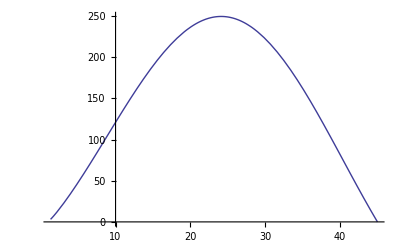

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,3.50854×10^-9},{44.8,3.60736×10^-9},{44.6,3.70364×10^-9},{44.4,3.80369×10^-9},{44.2,3.90682×10^-9},{44.,4.01306×10^-9},{43.8,4.12248×10^-9},{43.6,4.23498×10^-9},{43.4,4.35148×10^-9},{43.2,4.47129×10^-9},{43.,4.59469×10^-9},{42.8,4.72098×10^-9},{42.6,4.85386×10^-9},{42.4,4.98868×10^-9},{42.2,5.1295×10^-9},{42.,5.2711×10^-9},{41.8,5.41924×10^-9},{41.6,5.57305×10^-9},{41.4,5.72966×10^-9},{41.2,5.89224×10^-9},{41.,6.05985×10^-9},{40.8,6.23268×10^-9},{40.6,6.4112×10^-9},{40.4,6.59522×10^-9},{40.2,6.78512×10^-9},{40.,6.98128×10^-9},{39.8,7.1844×10^-9},{39.6,7.39251×10^-9},{39.4,7.60394×10^-9},{39.2,7.83076×10^-9},{39.,8.06061×10^-9},{38.8,8.29796×10^-9},{38.6,8.54307×10^-9},{38.4,8.79625×10^-9},{38.2,9.05773×10^-9},{38.,9.32784×10^-9},{37.8,9.60685×10^-9},{37.6,9.89524×10^-9},{37.4,1.01931×10^-8},{37.2,1.05011×10^-8},{37.,1.08195×10^-8},{36.8,1.1148×10^-8},{36.6,1.14881×10^-8},{36.4,1.18382×10^-8},{36.2,1.22033×10^-8},{36.,1.2579×10^-8},{35.8,1.29675×10^-8},{35.6,1.33692×10^-8},{35.4,1.37849×10^-8},{35.2,1.42149×10^-8},{35.,1.46598×10^-8},{34.8,1.51204×10^-8},{34.6,1.55964×10^-8},{34.4,1.60892×10^-8},{34.2,1.65992×10^-8},{34.,1.71271×10^-8},{33.8,1.76736×10^-8},{33.6,1.82393×10^-8},{33.4,1.8825×10^-8},{33.2,1.94315×10^-8},{33.,2.00595×10^-8},{32.8,2.071×10^-8},{32.6,2.13822×10^-8},{32.4,2.20861×10^-8},{32.2,2.28044×10^-8},{32.,2.35532×10^-8},{31.8,2.43292×10^-8},{31.6,2.51333×10^-8},{31.4,2.59666×10^-8},{31.2,2.68301×10^-8},{31.,2.77251×10^-8},{30.8,2.86529×10^-8},{30.6,2.96143×10^-8},{30.4,3.06116×10^-8},{30.2,3.16449×10^-8},{30.,3.27168×10^-8},{29.8,3.38281×10^-8},{29.6,3.49804×10^-8},{29.4,3.6176×10^-8},{29.2,3.74158×10^-8},{29.,3.87007×10^-8},{28.8,4.0036×10^-8},{28.6,4.1418×10^-8},{28.4,4.2853×10^-8},{28.2,4.43418×10^-8},{28.,4.58844×10^-8},{27.8,4.74883×10^-8},{27.6,4.91504×10^-8},{27.4,5.0875×10^-8},{27.2,5.26641×10^-8},{27.,5.45203×10^-8},{26.8,5.64462×10^-8},{26.6,5.84443×10^-8},{26.4,6.05182×10^-8},{26.2,6.26676×10^-8},{26.,6.48968×10^-8},{25.8,6.72094×10^-8},{25.6,6.96116×10^-8},{25.4,7.20989×10^-8},{25.2,7.46793×10^-8},{25.,7.73545×10^-8},{24.8,8.01277×10^-8},{24.6,8.30038×10^-8},{24.4,8.5982×10^-8},{24.2,8.90661×10^-8},{24.,9.22618×10^-8},{23.8,9.55715×10^-8},{23.6,9.89955×10^-8},{23.4,1.02538×10^-7},{23.2,1.06203×10^-7},{23.,1.09991×10^-7},{22.8,1.13905×10^-7},{22.6,1.17946×10^-7},{22.4,1.22116×10^-7},{22.2,1.26414×10^-7},{22.,1.3084×10^-7},{21.8,1.35399×10^-7},{21.6,1.40084×10^-7},{21.4,1.44896×10^-7},{21.2,1.49822×10^-7},{21.,1.54874×10^-7},{20.8,1.60028×10^-7},{20.6,1.65285×10^-7},{20.4,1.70633×10^-7},{20.2,1.76072×10^-7},{20.,1.81544×10^-7},{19.8,1.87067×10^-7},{19.6,1.92608×10^-7},{19.4,1.98132×10^-7},{19.2,2.03606×10^-7},{19.,2.08983×10^-7},{18.8,2.14218×10^-7},{18.6,2.19259×10^-7},{18.4,2.24012×10^-7},{18.2,2.28412×10^-7},{18.,2.32357×10^-7},{17.8,2.35726×10^-7},{17.6,2.38386×10^-7},{17.4,2.4018×10^-7},{17.2,2.40894×10^-7},{17.,2.40318×10^-7},{16.8,2.38202×10^-7},{16.6,2.34199×10^-7},{16.4,2.27918×10^-7},{16.2,2.19029×10^-7},{16.,2.06895×10^-7},{15.8,1.90933×10^-7},{15.6,1.70422×10^-7},{15.4,1.44473×10^-7},{15.2,1.12042×10^-7},{15.,7.18919×10^-8},{14.8,2.25397×10^-8},{14.6,-3.78436×10^-8},{14.4,-1.11364×10^-7},{14.2,-2.00631×10^-7},{14.,-3.08775×10^-7},{13.8,-4.39585×10^-7},{13.6,-5.9768×10^-7},{13.4,-7.88701×10^-7},{13.2,-1.01944×10^-6},{13.,-1.29841×10^-6},{12.8,-1.6359×10^-6},{12.6,-2.04473×10^-6},{12.4,-2.54073×10^-6},{12.2,-3.14358×10^-6},{12.,-3.87776×10^-6},{11.8,-4.77408×10^-6},{11.6,-5.87117×10^-6},{11.4,-7.21779×10^-6},{11.2,-8.87558×10^-6},{11.,-0.0000109232},{10.8,-0.0000134608},{10.6,-0.0000166169},{10.4,-0.0000205571},{10.2,-0.0000254952},{10.,-0.0000317085},{9.8,-0.0000395584},{9.6,-0.0000495172},{9.4,-0.0000622043},{9.2,-0.0000784345},{9.,-0.0000992829},{8.8,-0.000126171},{8.6,-0.00016098},{8.4,-0.000206204},{8.2,-0.000265147},{8.,-0.000342182},{7.8,-0.000443075},{7.6,-0.000575411},{7.4,-0.000749086},{7.2,-0.000976926},{7.,-0.00127537},{6.8,-0.00166525},{6.6,-0.00217254},{6.4,-0.00282919},{6.2,-0.00367374},{6.,-0.00475195},{5.8,-0.00611721},{5.6,-0.00783088},{5.4,-0.00996262},{5.2,-0.0125908},{5.,-0.015803}}

```mathematica
(*The imaginary part vs the radius*)
```

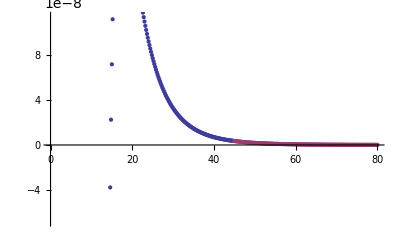

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

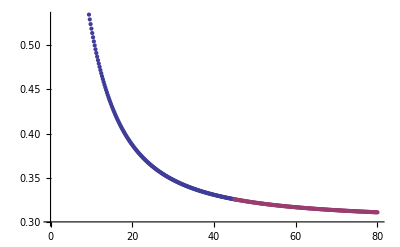

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.950/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.950/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.950/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio2.0/Q=0.950/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```